# Scara robot kinematic analisys DH convention

analisys kinematic robot Scara

convention DH

```mathematica
ClearAll["Global`*"]
```

-Graphics--Graphics-

## Position analysis: direct kinematics

Roto - translation matrix about z axis

```mathematica
Mrotztrasl[α_,point_]:={{Cos[α],-Sin[α],0,point[[1]]},{Sin[α],Cos[α],0,point[[2]]},{0,0,1,point[[3]]},{0,0,0,1}}
```

```mathematica
A={L1 Cos[θ1[t]],L1 Sin[θ1[t]],h,1}; (*in RF0*)
```

Mij is the matrix from j to i and it takes as arguments the relative angle and the origin and the rotation of j w.r.t. i

### M01

```mathematica
M01=Mrotztrasl[θ1[t],A];M01//MatrixForm  (*M from 1 to 0*)
```

(Cos[θ1[t]] | -Sin[θ1[t]] | 0 | L1 Cos[θ1[t]]
Sin[θ1[t]] | Cos[θ1[t]] | 0 | L1 Sin[θ1[t]]
0 | 0 | 1 | h
0 | 0 | 0 | 1)

```mathematica
P1={L2 Cos[θ2[t]],L2 Sin[θ2[t]],0,1};(*P in RF1*)
```

```mathematica
P=M01.P1//Simplify;P//MatrixForm (*P in RF0*)
```

(L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]
L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]
h
1)

### M12

```mathematica
M12=Mrotztrasl[θ2[t],P1];M12//MatrixForm (*M from 2 to 1*)
```

(Cos[θ2[t]] | -Sin[θ2[t]] | 0 | L2 Cos[θ2[t]]
Sin[θ2[t]] | Cos[θ2[t]] | 0 | L2 Sin[θ2[t]]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

### M02

```mathematica
M02=M01.M12//Simplify;M02//MatrixForm (*from 2 to 0*)
```

(Cos[θ1[t]+θ2[t]] | -Sin[θ1[t]+θ2[t]] | 0 | L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]
Sin[θ1[t]+θ2[t]] | Cos[θ1[t]+θ2[t]] | 0 | L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]
0 | 0 | 1 | h
0 | 0 | 0 | 1)

### M23

```mathematica
E2={0,0,-L[t],1};
```

```mathematica
M23=Mrotztrasl[0,E2];M23//MatrixForm(*from 3 to 2*)
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | -L[t]
0 | 0 | 0 | 1)

### M03

```mathematica
M03=M02.M23//Simplify;M03//MatrixForm (*from 3 to 0*)
```

(Cos[θ1[t]+θ2[t]] | -Sin[θ1[t]+θ2[t]] | 0 | L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]
Sin[θ1[t]+θ2[t]] | Cos[θ1[t]+θ2[t]] | 0 | L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]
0 | 0 | 1 | h-L[t]
0 | 0 | 0 | 1)

```mathematica
E3={0,0,0,1};
```

```mathematica
EE=M03.E3//Simplify;EE//MatrixForm (*E in RF0*)
```

(L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]
L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]
h-L[t]
1)

### Data

```mathematica
Data1={L1->0.3,L2->0.3,h->1,θ1[t]->0.2,θ2[t]->0.1,L[t]->0.3};
```

```mathematica
N@M03/.Data1//MatrixForm
```

(0.955336 | -0.29552 | 0. | 0.580621
0.29552 | 0.955336 | 0. | 0.148257
0. | 0. | 1. | 0.7
0. | 0. | 0. | 1.)

```mathematica
A3=Inverse[M03].A//Simplify;A3//MatrixForm (* M03^-1 = M30 *)
```

(-L2
0
L[t]
1)

```mathematica
W03.A//Simplify//MatrixForm
```

W03.{L1 Cos[θ1[t]],L1 Sin[θ1[t]],h,1}

```mathematica
P2=Inverse@M02.P//Simplify
```

{0,0,0,1}

## Inverse kinematics

```mathematica
M03d=Mrotztrasl[ψd,{xd,yd,zd}];M03d//MatrixForm
```

(Cos[ψd] | -Sin[ψd] | 0 | xd
Sin[ψd] | Cos[ψd] | 0 | yd
0 | 0 | 1 | zd
0 | 0 | 0 | 1)

```mathematica
M03//MatrixForm
```

(Cos[θ1[t]+θ2[t]] | -Sin[θ1[t]+θ2[t]] | 0 | L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]
Sin[θ1[t]+θ2[t]] | Cos[θ1[t]+θ2[t]] | 0 | L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]
0 | 0 | 1 | h-L[t]
0 | 0 | 0 | 1)

```mathematica
RotBlock=M03[[1;;3,1;;3]];RotBlock//MatrixForm
M03d[[1;;3,1;;3]]//MatrixForm
```

(Cos[θ1[t]+θ2[t]] | -Sin[θ1[t]+θ2[t]] | 0
Sin[θ1[t]+θ2[t]] | Cos[θ1[t]+θ2[t]] | 0
0 | 0 | 1)

(Cos[ψd] | -Sin[ψd] | 0
Sin[ψd] | Cos[ψd] | 0
0 | 0 | 1)

We need both cosine and sine equations since a single equation would produce multiple solutions and then we have to discriminate with a second trigonometric equation.

```mathematica
SetofEqns={RotBlock[[1,1]]==M03d[[1,1]],RotBlock[[1,2]]==M03d[[1,2]]};SetofEqns//MatrixForm
```

(Cos[θ1[t]+θ2[t]]==Cos[ψd]
-Sin[θ1[t]+θ2[t]]==-Sin[ψd])

```mathematica
Solve[SetofEqns,{θ1[t],θ2[t]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{θ2[t]→ConditionalExpression[ArcTan[Cos[ψd],Sin[ψd]]+2 π C[1]-θ1[t], C[1]∈ℤ]}}

```mathematica
EQI=Reduce[SetofEqns,{θ1[t],θ2[t]}]
```

C[1]∈ℤ&&((√(1-Cos[ψd]^2)≠0&&((Sin[ψd]==-√(1-Cos[ψd]^2)&&θ2[t]==2 ArcTan[(-1+Cos[ψd])/(√(1-Cos[ψd]^2))]+2 π C[1]-θ1[t])||(Sin[ψd]==√(1-Cos[ψd]^2)&&θ2[t]==2 ArcTan[(1-Cos[ψd])/(√(1-Cos[ψd]^2))]+2 π C[1]-θ1[t])))||(Cos[ψd]==1&&Sin[ψd]==0&&θ2[t]==2 π C[1]-θ1[t])||(Cos[ψd]==-1&&Sin[ψd]==0&&θ2[t]==π+2 π C[1]-θ1[t]))

```mathematica
EQII=EE[[1]]==M03d[[1,4]]
EQIII=EE[[2]]==M03d[[2,4]]
EQIIII=EE[[3]]==M03d[[3,4]]
```

L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]==xd

L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]==yd

h-L[t]==zd

```mathematica
Data2={L1->0.3,L2->0.3,h->1,xd->0.4,yd->0.4,zd->0.4};
```

```mathematica
KinSol2=Solve[{EQII,EQIII,EQIIII}/.Data2,{θ1[t],θ2[t],L[t]}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ1[t]→0.445561,θ2[t]→0.679674,L[t]→0.6},{θ1[t]→1.12524,θ2[t]→-0.679674,L[t]→0.6}}

The choice of the orientation is only given by ψd = θ1+θ2 and the the choice of θ1 and θ2 is up to us. If we give a specific position, the controller has to choose 1 of the 2 possible solution where the θ1, θ2 and L are defined.

```mathematica
Solve[EQI/.KinSol2[[1]],ψd][[1]]/.{C[1]->0,C[2]->0}
Solve[EQI/.KinSol2[[2]],ψd][[1]]/.{C[1]->0,C[2]->0}
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::ztest1: Unable to decide whether numeric quantity -Tan[64490991/114626699]+Cos[128981982/114626699] Tan[64490991/114626699]+Tan[64490991/114626699]^3+Cos[128981982/114626699] Tan[64490991/114626699]^3 is equal to zero. Assuming it is.

{ψd→1.12524}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::ztest1: Unable to decide whether numeric quantity -Tan[6897337/30960219]+Cos[13794674/30960219] Tan[6897337/30960219]+Tan[6897337/30960219]^3+Cos[13794674/30960219] Tan[6897337/30960219]^3 is equal to zero. Assuming it is.

{ψd→0.445561}

Clearly ψd is constrained to be one of the two possible values allowed by either solution1 or 2 of KinSol2. Therefore it is not possible to satisfy position and orientation of the end effector (in this case, 4 dofs) with the allowable kinematics (3 dofs).
We take the first solution of KinSol2

```mathematica
KinSol=KinSol2[[1]]
```

{θ1[t]→0.445561,θ2[t]→0.679674,L[t]→0.6}

```mathematica
Data3={L1->0.3,L2->0.3,h->1,xd->0.4,zd->0.4,ψd->π/4};
```

```mathematica
KinSol3=Solve[{RotBlock[[1,1]]==M03d[[1,1]],RotBlock[[1,2]]==M03d[[1,2]],EE[[1]]==xd,EE[[3]]==zd}/.Data3,{θ1[t],θ2[t],L[t]}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ1[t]→-0.894093,θ2[t]→1.67949,L[t]→0.6},{θ1[t]→0.894093,θ2[t]→-0.108694,L[t]→0.6}}

### Sketch of the robot

```mathematica
Data4={L1->0.3,L2->0.3,h->1};
```

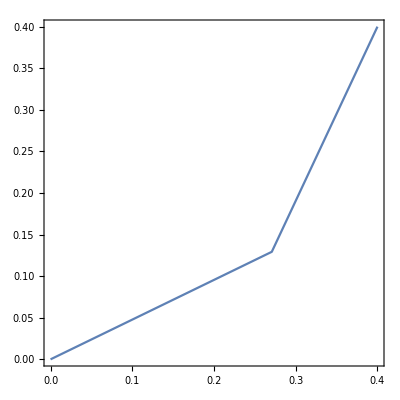

```mathematica
AN=N[A/.KinSol/.Data4][[1;;2]];
PN=N[P/.KinSol/.Data4][[1;;2]];
ListLinePlot[{{0,0},{AN[[1]],AN[[2]]},{PN[[1]],PN[[2]]}},Frame->True,AspectRatio->1]
```

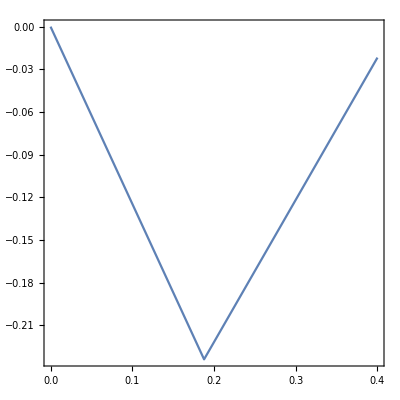

```mathematica
AN3=N[A/.KinSol3[[1]]/.Data4][[1;;2]];
PN3=N[P/.KinSol3[[1]]/.Data4][[1;;2]];
plot1=ListLinePlot[{{0,0},{AN3[[1]],AN3[[2]]},{PN3[[1]],PN3[[2]]}},Frame->True,AspectRatio->1]
```

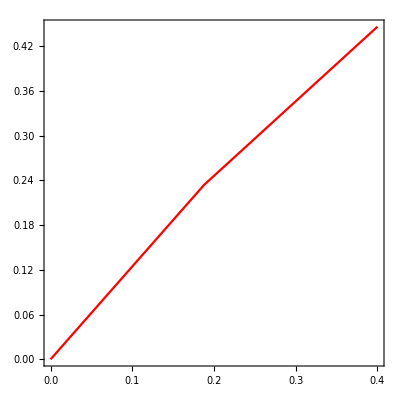

```mathematica
AN4=N[A/.KinSol3[[2]]/.Data4][[1;;2]];
PN4=N[P/.KinSol3[[2]]/.Data4][[1;;2]];
plot2=ListLinePlot[{{0,0},{AN4[[1]],AN4[[2]]},{PN4[[1]],PN4[[2]]}},Frame->True,PlotStyle->Red,AspectRatio->1]
```

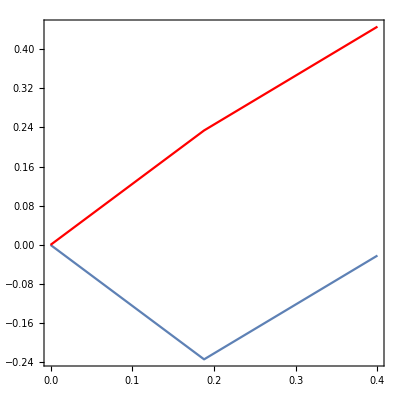

```mathematica
Show[{plot1,plot2},PlotRange->Automatic]
```

## Velocity analysis: direct kinematics

```mathematica
W01=Simplify[(D[M01, t]).Inverse@M01];W01//MatrixForm
```

(0 | -θ1'[t] | 0 | 0
θ1'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Infinitesimal elicoidal roto - translation matrix of a revolute joint (z - axis) :

```mathematica
Lrot={{0,-1,0,0},{1,0,0,0},{0,0,0,0},{0,0,0,0}};Lrot//MatrixForm
```

(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
L01=Lrot;
W01==L01*D[θ1[t], t]//Simplify
```

True

Absolute velocity of point A (body fixed to frame 1), projected in frame 0 :

```mathematica
W01.A//MatrixForm
```

(-L1 Sin[θ1[t]] θ1'[t]
L1 Cos[θ1[t]] θ1'[t]
0
0)

Velocity matrix of link 2 produced only by the joint between links 1 and 2 (i . e ., relative velocity matrix of frame 2 w.r.t. frame 1), expressed in frame 1 :

```mathematica
W12F1=(D[M12, t]).Inverse@M12//Simplify;W12F1//MatrixForm
```

(0 | -θ2'[t] | 0 | 0
θ2'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Relative velocity of P w.r.t. RF1

```mathematica
W12F1.P1//Simplify//MatrixForm
```

(-L2 Sin[θ2[t]] θ2'[t]
L2 Cos[θ2[t]] θ2'[t]
0
0)

W12F1 is projected in frame 0 and still describes the motion of link 2 w.r.t. link 1. Then you have to use points projected in frame 0.

```mathematica
W12=M01.W12F1.Inverse@M01//Simplify;W12//MatrixForm
```

(0 | -θ2'[t] | 0 | L1 Sin[θ1[t]] θ2'[t]
θ2'[t] | 0 | 0 | -L1 Cos[θ1[t]] θ2'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W12.P//Simplify//MatrixForm
```

(-L2 Sin[θ1[t]+θ2[t]] θ2'[t]
L2 Cos[θ1[t]+θ2[t]] θ2'[t]
0
0)

M01 * W12F1 * P1 = M01 * ^1(VP1) = ^0(VP1)

```mathematica
M01.W12F1.P1//Simplify//MatrixForm
```

(-L2 Sin[θ1[t]+θ2[t]] θ2'[t]
L2 Cos[θ1[t]+θ2[t]] θ2'[t]
0
0)

Infinitesimal elicoidal rototranslation matrix of link 2 with respect to link 1, expressed in frame 1

```mathematica
L12F1=Lrot
```

{{0,-1,0,0},{1,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
L12F1*D[θ2[t], t]//MatrixForm
L12F1*D[θ2[t], t]==W12F1
```

(0 | -θ2'[t] | 0 | 0
θ2'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

True

```mathematica
L12=M01.L12F1.Inverse@M01//Simplify;L12//MatrixForm
```

(0 | -1 | 0 | L1 Sin[θ1[t]]
1 | 0 | 0 | -L1 Cos[θ1[t]]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

The velocity of point A produced by the joint from link 1 to 2 is zero

```mathematica
W12.A
```

{0,0,0,0}

```mathematica
W01.A//MatrixForm
```

(-L1 Sin[θ1[t]] θ1'[t]
L1 Cos[θ1[t]] θ1'[t]
0
0)

```mathematica
W23F2=(D[M23, t]).Inverse[M23];W23F2//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -L'[t]
0 | 0 | 0 | 0)

```mathematica
W03.P//Simplify//MatrixForm
```

W03.{L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]],L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]],h,1}

```mathematica
W02.P//MatrixForm
```

W02.{L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]],L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]],h,1}

{0, 0, -L'[t]} is the velocity of a point of RF3 that overlaps the origin of RF2. It’s NOT  the velocity of the origin of RF3.

```mathematica
W23=M02.W23F2.Inverse@M02;W23//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -L'[t]
0 | 0 | 0 | 0)

```mathematica
W23//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -L'[t]
0 | 0 | 0 | 0)

```mathematica
Ltraslz={{0,0,0,0},{0,0,0,0},{0,0,0,1},{0,0,0,0}};Ltraslz//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0)

```mathematica
L23F2=-Ltraslz;
```

```mathematica
W23F2=L23F2*D[L[t], t]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,-L'[t]},{0,0,0,0}}

```mathematica
L23=M02.L23F2.Inverse@M02;L23//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 0 | 0)

Rival’s theorem

```mathematica
W02=W01+W12;W02//MatrixForm
```

(0 | -θ1'[t]-θ2'[t] | 0 | L1 Sin[θ1[t]] θ2'[t]
θ1'[t]+θ2'[t] | 0 | 0 | -L1 Cos[θ1[t]] θ2'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W02.A//Simplify//MatrixForm
```

(-L1 Sin[θ1[t]] θ1'[t]
L1 Cos[θ1[t]] θ1'[t]
0
0)

The last column of W03 is the velocity of a point of RF3 that overlaps the origin of RF0. The rotation block contains the angular velocities.

```mathematica
W03=W01+W12+W23//Simplify;W03//MatrixForm
```

(0 | -θ1'[t]-θ2'[t] | 0 | L1 Sin[θ1[t]] θ2'[t]
θ1'[t]+θ2'[t] | 0 | 0 | -L1 Cos[θ1[t]] θ2'[t]
0 | 0 | 0 | -L'[t]
0 | 0 | 0 | 0)

```mathematica
VE=W03.EE//Simplify;VE//MatrixForm
```

(-((L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]) θ1'[t])-L2 Sin[θ1[t]+θ2[t]] θ2'[t]
(L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]) θ1'[t]+L2 Cos[θ1[t]+θ2[t]] θ2'[t]
-L'[t]
0)

```mathematica
W03.A//Simplify
```

{-L1 Sin[θ1[t]] θ1'[t],L1 Cos[θ1[t]] θ1'[t],-L'[t],0}

```mathematica
W23.P
```

{0,0,-L'[t],0}

```mathematica
W12.A
```

{0,0,0,0}

```mathematica
W02F2=Inverse@M02.W02.M02;
```

```mathematica
W23.P
```

{0,0,-L'[t],0}

## Velocity analysis : inverse kinematics

The inverse kinematic problem finds the joint velocities required to produce a given velocity matrix of the end effector (link 3).
In the inverse kinematics we want to find the joint velocities required to produce a given velocity configuration of the end effector . The problem is linear in the joint velocities, which can be collected in the Jacobian.

We want to set the translation and angular velocities . We have 4 equation in 3 unknowns (joint cooridinates)

```mathematica
eqs={VE[[1]]-VX,VE[[2]]-VY,VE[[3]]-VZ,W03[[1,2]]-(-ωz)}//Simplify;eqs//MatrixForm
```

(-VX-(L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]) θ1'[t]-L2 Sin[θ1[t]+θ2[t]] θ2'[t]
-VY+(L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]) θ1'[t]+L2 Cos[θ1[t]+θ2[t]] θ2'[t]
-VZ-L'[t]
ωz-θ1'[t]-θ2'[t])

```mathematica
vels={D[θ1[t], t],D[θ2[t], t],D[L[t], t]};vels//MatrixForm
```

(θ1'[t]
θ2'[t]
L'[t])

```mathematica
Jac=Normal@CoefficientArrays[eqs,vels][[2]];Jac//MatrixForm
```

(-L1 Sin[θ1[t]]-L2 Sin[θ1[t]+θ2[t]] | -L2 Sin[θ1[t]+θ2[t]] | 0
L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]] | L2 Cos[θ1[t]+θ2[t]] | 0
0 | 0 | -1
-1 | -1 | 0)

Inverse kinematics for velocities : over-constrained problem, 4 equations (3 velocity components of point E plus absolute angular rate of frame 3) with 3 unknowns (θ1’[t], θ2’[t], L’[t])

```mathematica
RotJac=Jac[[1;;3,1;;3]];RotJac//MatrixForm
```

(-L1 Sin[θ1[t]]-L2 Sin[θ1[t]+θ2[t]] | -L2 Sin[θ1[t]+θ2[t]] | 0
L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]] | L2 Cos[θ1[t]+θ2[t]] | 0
0 | 0 | -1)

```mathematica
jointvel=(Inverse@RotJac).{VX,VY,VZ}//Simplify;jointvel//MatrixForm
```

((Csc[θ2[t]] (VX Cos[θ1[t]+θ2[t]]+VY Sin[θ1[t]+θ2[t]]))/L1
-(Csc[θ2[t]] (L1 VX Cos[θ1[t]]+L2 VX Cos[θ1[t]+θ2[t]]+L1 VY Sin[θ1[t]]+L2 VY Sin[θ1[t]+θ2[t]]))/(L1 L2)
-VZ)

```mathematica
N[jointvel] /. {VX ->1, VY->1, VZ->1, L1->0.3, L2->0.3, h->1} /. KinSol
```

{7.07107,-14.1421,-1.}

Definition of Auxiliary Reference Frame : a frame centered in the EE with axes parallel to the fixed frame

```mathematica
M0a={{1,0,0,EE[[1]]},{0,1,0,EE[[2]]},{0,0,1,EE[[3]]},{0,0,0,1}};M0a//MatrixForm
```

(1 | 0 | 0 | L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]
0 | 1 | 0 | L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]
0 | 0 | 1 | h-L[t]
0 | 0 | 0 | 1)

```mathematica
L01Fa=Inverse[M0a].L01.M0a//Simplify;L01Fa//MatrixForm
W01Fa=L01Fa D[θ1[t], t]//Simplify;W01Fa//MatrixForm
```

(0 | -1 | 0 | -L1 Sin[θ1[t]]-L2 Sin[θ1[t]+θ2[t]]
1 | 0 | 0 | L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | -θ1'[t] | 0 | -((L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]) θ1'[t])
θ1'[t] | 0 | 0 | (L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]) θ1'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
L12Fa=Inverse[M0a].L12.M0a//Simplify;L12Fa//MatrixForm
W12Fa=L12Fa D[θ2[t], t];W12Fa//MatrixForm
```

(0 | -1 | 0 | -L2 Sin[θ1[t]+θ2[t]]
1 | 0 | 0 | L2 Cos[θ1[t]+θ2[t]]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | -θ2'[t] | 0 | -L2 Sin[θ1[t]+θ2[t]] θ2'[t]
θ2'[t] | 0 | 0 | L2 Cos[θ1[t]+θ2[t]] θ2'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
L23Fa=Inverse[M0a].L23.M0a//Simplify;L23Fa//MatrixForm
W23Fa=L23Fa D[L[t], t];W23Fa//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -L'[t]
0 | 0 | 0 | 0)

W03Fa collects in a single matrix all the velocities of the end effector (angular and linear), differently from W03

```mathematica
W03Fa=W01Fa+W12Fa+W23Fa//Simplify;W03Fa//MatrixForm
```

(0 | -θ1'[t]-θ2'[t] | 0 | -((L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]) θ1'[t])-L2 Sin[θ1[t]+θ2[t]] θ2'[t]
θ1'[t]+θ2'[t] | 0 | 0 | (L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]) θ1'[t]+L2 Cos[θ1[t]+θ2[t]] θ2'[t]
0 | 0 | 0 | -L'[t]
0 | 0 | 0 | 0)

```mathematica
Inverse@M03.W03.M03//Simplify//MatrixForm
```

(0 | -θ1'[t]-θ2'[t] | 0 | L1 Sin[θ2[t]] θ1'[t]
θ1'[t]+θ2'[t] | 0 | 0 | (L2+L1 Cos[θ2[t]]) θ1'[t]+L2 θ2'[t]
0 | 0 | 0 | -L'[t]
0 | 0 | 0 | 0)

```mathematica
invproblem=Solve[{W03Fa[[1,4]]==VX,W03Fa[[2,4]]==VY,W03Fa[[3,4]]==VZ},vels]//Simplify;MatrixForm[invproblem,TableDirections->Row]
```

(θ1'[t]→(Csc[θ2[t]] (VX Cos[θ1[t]+θ2[t]]+VY Sin[θ1[t]+θ2[t]]))/L1
θ2'[t]→-(Csc[θ2[t]] (L1 VX Cos[θ1[t]]+L2 VX Cos[θ1[t]+θ2[t]]+L1 VY Sin[θ1[t]]+L2 VY Sin[θ1[t]+θ2[t]]))/(L1 L2)
L'[t]→-VZ)